## Funkcije

```mathematica
Funkcije geometrije
```

```mathematica
(* Računanje števila in dimenzije segmentov v strukturi *)
izracunajSegmenteSirine[s_,d_,n_]:=Module[
{hPrib, nPrib,nS, hS},
(* Iskanje ustrezne širine in število segmentov *)
hPrib = (4 s + 2 d)/n; (* Prib. dolžina segmenta *)
nPrib = s/hPrib;  (* Prib. št. segmentov na polovici širine *)
nS = Round[nPrib]; (* Točno št. segmentov na pol. šir. *)
hS = s/nS; (* Točna, ustrezna dolžina segmenta širine *)
Return[{hS, nS}] (* Vrne seznam {dolžina segmenta širine, število segmentov na polovici širine} *)
]

izracunajSegmenteDebeline[s_,d_,n_]:=Module[
{hPrib, nPrib,nD, hD},
hPrib= (4 s + 2 d)/n; (* Približna dolžina segmenta *)
nPrib = d/hPrib; (* Približno število segmentov na eni debelini *)
nD = Round[nPrib]; (* Točno število segmentov na eni debelini *)
hD = d/nD;  (* Točna, ustrezna dolžina segmenta debeline *)
Return[{hD, nD}] (* Vrne seznam {dolžina segmenta debeline, število segmentov na debelini} *)
]

(* Risanje točk v strukturi *)
izracunajTockePravokotnika[s_,d_,n_, H0_, brezVrha_, brezDna_, izbrisaneTockeVrha_]:=Module[
{hS,hD,nS,nD,xKoord, yKoord, i, tockeStrukture, stSegKoncno},   (* Seznam lokalnih spremenljivk v tem modulu *)
(* Pomen argumentov:;
s -> polovica širine objekta;
d -> debelina objekta;
n -> približno število segmentov na strukturi;
H0 -> offset strukture po Y osi;
brezVrha -> Če je true, izpusti točke zgornje stranice pravokotnika;
brezDna -> Če je true, izpusti točke spodnje stranice pravokotnika;
izbrisaneTockeVrha -> Če ni 0, naj izbriše točke na vrhu, ki so od simetrale oddaljene manj ali za to dolžino. 
Glej *** na skici. To se uporablja za izpuščanje točk na substratu, za pripravo meje substr.-prevodnik. *)

(* Izračun sledečih podatkov:;
hS -> dolžina segmenta širine;
hD -> dolžina segmenta debeline;
nS -> št. segmentov po polovici širine;
nD -> št. segmentov po debelini;
*)

(* SKICA:
       3;
  ----***|***----
|                |
| 4              | 2
|                |
 -------|-------;
      5         1
*)
{hS, nS}=izracunajSegmenteSirine[s,d,n];
{hD, nD}=izracunajSegmenteDebeline[s,d,n];

Switch[{brezVrha, brezDna}, 
{False, False}, (* Z VRHOM IN DNOM *)
(* izračun X koordinat *)
xKoord=Table[i*hS-hS/2, {i,1,nS}]; (* 1  *)
xKoord=Join[xKoord,Table[s, {i,1,nD}]]; (* 2  *)
xKoord=Join[xKoord,Table[s-i hS+hS/2, {i,1,2 nS}]]; (* 3  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
xKoord=Join[xKoord,Table[-s+i hS-hS/2, {i,1,nS}]]; (* 5 *)
(* izračun Y koordinat *)
yKoord=Table[H0, {i,1,nS}]; (* 1  *)
yKoord=Join[yKoord,Table[H0+i hD-hD/2, {i,1,nD}]]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d, {i,1,2 nS}]]; (* 3  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]]; (* 4 *)
yKoord=Join[yKoord,Table[H0, {i,1,nS}]], (* 5 *)
{False, True}, (* BREZ DNA *)
(* izračun X koordinat *)
xKoord=Table[s, {i,1,nD}]; (* 2  *)
xKoord=Join[xKoord,Table[s-i hS+hS/2, {i,1,2 nS}]]; (* 3  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
(* izračun Y koordinat *)
yKoord=Table[H0+i hD-hD/2, {i,1,nD}]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d, {i,1,2 nS}]]; (* 3  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]],(* 4 *)
{True, False}, (* BREZ VRHA *)
(* izračun X koordinat *)
xKoord=Table[i*hS-hS/2, {i,1,nS}]; (* 1  *)
xKoord=Join[xKoord,Table[s, {i,1,nD}]]; (* 2  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
xKoord=Join[xKoord,Table[-s+i hS-hS/2, {i,1,nS}]]; (* 5 *)
(* izračun Y koordinat *)
yKoord=Table[H0, {i,1,nS}]; (* 1  *)
yKoord=Join[yKoord,Table[H0+i hD-hD/2, {i,1,nD}]]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]]; (* 4 *)
yKoord=Join[yKoord,Table[H0, {i,1,nS}]],(* 5 *)
{True, True}, (* BREZ VRHA IN DNA *)
(* izračun X koordinat *)
xKoord=Table[s, {i,1,nD}]; (* 2  *)
xKoord=Join[xKoord,Table[-s, {i,1,nD}]]; (* 4 *)
(* izračun Y koordinat *)
yKoord=Table[H0+i hD-hD/2, {i,1,nD}]; (* 2  *)
yKoord=Join[yKoord,Table[H0+d-i hD+hD/2, {i,1,nD}]];(* 4 *)
]
(* Sestavi obe koordinati *);
tockeStrukture=Table[{xKoord[[i]],yKoord[[i]]}, {i,1, Length[xKoord]}]//N;

(* Izračunaj število segmentov *)
stSegKoncno = Length[tockeStrukture]; 
Return[{tockeStrukture,hS,hD, stSegKoncno}]
]


vrniVektorRazdalje[{xi_, yi_}, {xj_, yj_}]:=Module[
{},
Return[{(xj-xi),(yj-yi)}]
]

vrniZrcaljenVektorRazdalje[{xi_, yi_}, {xj_, yj_}]:=Module[
{},
Return[{(xj-xi),(yj+yi)}]
]


vrniKoteNormalSegmentov[obj_]:=Module[
{a, b, v, fiTan, fiNorm, fiArr,i},
(*Gre čez točke objekta, na podlagi sosednjih točk izračuna ;
kot normalnega vektorja glede na x os grafa. Ker predvidevamo ostre;
robove objektov, na koncu gre čez kote in popravi zaobljene robove.;
Za argument prejme matriko točk objekta {{x1,y1},{x2,y2},..};
Vrne matriko kotov normal v vseh središčih segmentov.*)
fiArr=Table[0, {i,1,Length[obj]}];

For[i=1, i<=(Length[obj]), i++,
Which[i==1,a=obj[[2]]; b=obj[[3]], (*Če je to 1. segment, naj raje vzame naslednji dve točki, ker segment 0 ne obstaja*)
i==Length[obj],a=obj[[i-2]]; b=obj[[i-1]], (*Če je to zadnji segment, naj raje vzame predzadnja dva, ne pa i+1 segment*)
True, a=obj[[i-1]]; b=obj[[i+1]]; (*Else, za vse običajne primere*)
];
v=vrniVektorRazdalje[a,b]; (*Vrne vektor od a do b*)
fiTan=ArcTan[v[[1]], v[[2]]];
fiNorm = Mod[(fiTan-Pi/2), (2 Pi)];
fiArr[[i]]=fiNorm;
];
(*Popravljanje zaobljenih robov*)
For[i=2, i<=(Length[fiArr]-2), i++,
If[fiArr[[i-1]]!=fiArr[[i]] && fiArr[[i]]!=fiArr[[i+1]]&&fiArr[[i+1]]!=fiArr[[i+2]], (*Če so štirje koti zaporedoma različni, je to koleno *)
fiArr[[i]]=fiArr[[i-1]]; fiArr[[i+1]]=fiArr[[i+2]]; (*Popravi nepravilna kota v kolenu na sosednje vrednosti*)
];
];

Return[fiArr];
];


vrniNormalneVektorjeSegmentov[obj_]:=Module[
(* Vrne seznam enotskih normalnih vektorjev za posamezne segmente objekta *)
{vectArr, angleArr,centerPoint, vectorEnd, currentVector,i },
angleArr=vrniKoteNormalSegmentov[obj];
vectArr = Table[0, {i,1, Length[obj]}];
For[i=1, i<=Length[obj], i++,
centerPoint=obj[[i]];(*rep vektorja*)
vectorEnd={centerPoint[[1]]+1 Cos[angleArr[[i]]], centerPoint[[2]]+1 Sin[angleArr[[i]]] };(*Glava vektorja*)
currentVector = {centerPoint, vectorEnd}; (*Končni vektor normale iz središča segmenta*)
(*Print["Norma normalnega vektorja ",currentVector, " je ", ((Sqrt[(vectorEnd[[2]]-centerPoint[[2]])^2+(vectorEnd[[1]]-centerPoint[[1]])^2])//N)];*)
vectArr[[i]]=currentVector;
];
Return[vectArr];
];
```

```mathematica
Funkcije za pripravo matrik
```

```mathematica
vrniVektorB[potencialTraku_, n_,m_]:=Module[
(* Vrne sestavljen vektor b v enačbi Ax=b;
n -> število segmentov prevodnika;
m -> število segmentov dielektrika;*)
{},Return[Table[If[i<=n, potencialTraku, 0], {i, 1, n+m}]];
];

vrniZgornjoMatrikoA[tockeTrak_, tockeSubst_, ]:=Module[
(* Vrne zgornji del matrike A v enačbi Ax=b, torej elemente za prevodnik *)
{},
Return[];
];

vrniMatrikoA[]:=Module[
(* Vrne sestavljeno matriko A v enačbi Ax=b *)
{},
Return[];
]
```

```mathematica
(*======================================================================================================*)
```

58

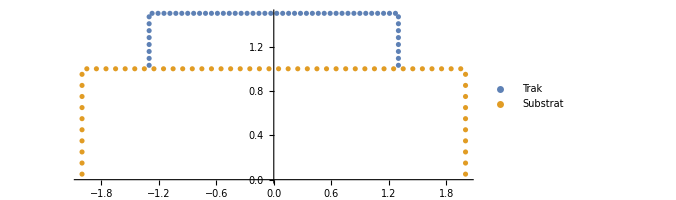

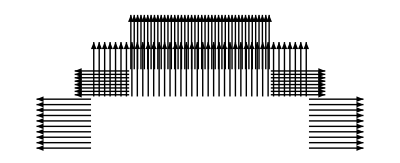

```mathematica
(* MAIN *)

(* Podane vrednosti *)
sSubs = 2; (* Širina substrata *)
dSubs = 1; (* Debelina substrata *)
nSubsPrib = 100; (* Približno število segmentov po celem pravokotnem objektu. To vrednost kasneje popravim na resnično število segmentov. *)
sTrak = 1.3;
dTrak = 0.5;
nTrakPrib = 100;
ϵr= 10; (* Epsilon relativni za substrat*)

(* Generirane spremenljivke *)
hSTrak; hDTrak; (* Širine segmentov traka - prevodnika - po širini in debelini *)
nTrak (* Število segmentov traka - prevodnika*)
hSSubs; hDSubs;(* Isto, a za substrat *)
nSubs;

(* Generiranje osnovnih točk in matrik*)
{tockeTrak,hSTrak,hDTrak, nTrak}  = izracunajTockePravokotnika[sTrak, dTrak, nTrakPrib, dSubs, False, True];
{tockeSubst,hSSubs,hDSubs, nSubs} = izracunajTockePravokotnika[sSubs,dSubs,nSubsPrib, 0, False, True];
normaleTrak=vrniNormalneVektorjeSegmentov[tockeTrak];
normaleSubst=vrniNormalneVektorjeSegmentov[tockeSubst];



(*Risanje*)
ListPlot[{tockeTrak, tockeSubst},PlotLegends->{"Trak","Substrat"}, AspectRatio->Automatic]
drawNormTrak=Table[Arrow[normaleTrak[[i]]], {i,1,Length[normaleTrak]}];
drawNormSubst=Table[Arrow[normaleSubst[[i]]], {i, 1, Length[normaleSubst]}];
Graphics[{drawNormTrak, drawNormSubst}]
```